# John Wesley McDonald Hayhurst

## Mathematica Assignment 1

Part #1: Understanding Population Models

### 1) By hand, use Separation of Variables to find the general solution for the equation dP/dt = rP(t). Be sure to indicate if there are any singular solutions. Attached is the by hand solution of the equation. This is confirmed by mathematica

```mathematica
f[t_,P_]=r*P[t]
```

r P[t]

```mathematica
DSolve[P'[t]==f[t,P],P[t],t]
```

{{P[t]→ⅇ^(r t) C[1]}}

### 2) Assume that the birth rate is 3.24% and the death rate is 1.97%. Find the particular solution for the initial value problem given below dP/dt = rP(t) P(0) = 6.084

```mathematica
DSolve[{P'[t]==f[t,P],P[0]==6.084},P[t],t]
```

{{P[t]→6.084 ⅇ^(r t)}}

This tells us that the constant for our model is 6.084, our r is equal to the birth rate minus the death rate which we know are 3.24% and 1.97% percent respectively giving us our r to be 1.27% or 0.0127. With this knowledge our solution looks like this

P(t)=6.084 e^(0.0127t)

### 3) Consider a population of pandas whose population P (in thousands of pandas) at time t (in years, where t = 0 corresponds to the year 2000). Data for the population of pandas is given. Explain why the value for r, given by the assumed birth and death rates, is reasonable.

The numbers are reasonable given that the rate of the population is growing at a constant 1.27%, at the year 2000 we know that the population will be at 6.084. since the death rate is lower than the birth rate the population will slowly increase. This is reflected by the growing panda population rates

### 4) Plot the population data and the model

```mathematica
g[t_]=6.084 ⅇ^(0.0127*t)
```

6.084 ⅇ^(0.0127 t)

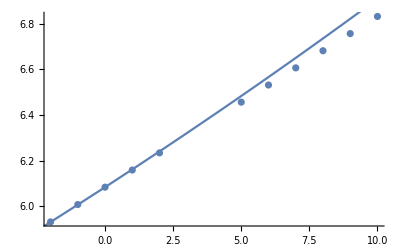

```mathematica
Show[ListPlot[{{-2,5.932},{-1,6.008},{0,6.084},{1, 6.159},{2,6.234},{5,6.456},{6, 6.531},{7, 6.606},{8,6.681}, {9, 6.756},{10, 6.831}}],Plot[g[x],{x,-4,12}]]
```

### 5) Use your model to predict the population of the pandas in the year 2500

Using 2000 as t = 0. t = 500 would be 2500. Knowing this plugging in 500 for t we get 3483.05 pandas.

```mathematica
g[500]
```

3483.05

### 6) Do you think your model is reasonable? What assumptions are you making by using an exponential model in terms of the rate of growth and population size? What factors are you not taking into consideration when using this model? Explain in paragraph form.

The model is relativly reasonable, in the fact that it will match our data from the given year and population. We assume that the birth and death rates do not change year by year and are consistant. We assume that the pandas will die and can be born. The factors that we are not taking into consideration in this model are that death and birth rates are different year to year, an unforseen event that will cause the death rate to increase, or the pandas are not able to give birth, and they do not have any predators.

### 7) By hand, show that the general solution for the equation dP/dt= rP(t)(N-P(t))

The bottom of the notebook has all hand written solutions attached

### 8) Suppose that the carrying capacity for pandas in their natural environment is N = 12.5 million and the intrinsic growth rate r is .2%. Plot the slope field associated with the differential equation. Use the slope field to answer the following questions.00 5 .14 x .14 150). Use the slope .0celd to answer the following questions:

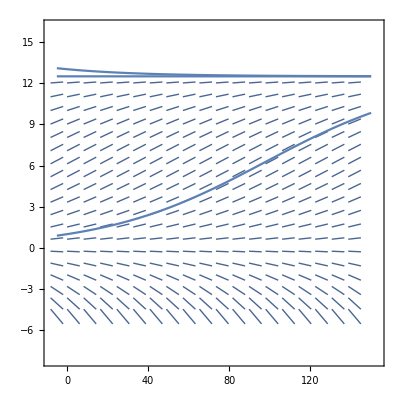

```mathematica
Show[VectorPlot[{1,.002*y*(12.5-y)},{x,-5,150},{y,-5,13},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20] ,Plot[12.5/(0*ⅇ^(-.002*x *12.5)+1),{x,-5,150}], Plot[12.5/(-0.04*ⅇ^(-.002*x *12.5)+1),{x,-5,150}],Plot[12.5/(11.5*ⅇ^(-.002*x *12.5)+1),{x,-5,150}]]
```

#### B) If P(0) > 12.5 = N, explain the behavior of the solution for -infinity < t < infinity; in particular, will the solution exist everywhere

The solution will start above the population limit of the environment so the population will start off higher than the limit and then will eventually reach the limit of the population and stay there. The solution will exist anywhere above 12.5 and no where below 12.5 as the population is growing but is being cut off by the limit of the of the environment

#### C) if 0 < P(0) < 12.5 = N, explain the behavior of the solution for -infinity < t < infinity; in particular, will the solution exist everywhere

The solution will start at the initial population and then it will slowly rise to reach the limit of the environment and stay steady there. The solution will exist everywhere between 0 and 12.5 and will never exist above 12.5 and below 0

#### D) if P(0) = 12.5 = N, explain the behavior of the solution for -infinity < t < infinity; in particular, will the solution exist everywhere

The solution will start at the inititial population which is the same as the population limit, the population will not grow and will not decrease as the population is constantly growing but also dying off at the rate to keep the environment limit satisfied. The solution will only exist at 12.5

#### E) if P(0) = 0, explain the behavior of the solution for -infinity < t < infinity; in particular, will the solution exist everywhere

The solution will start off at zero and continue to stay at zero because the population can not increase from zero, the solution does not also support the population being zero, the solution will only exist at 0

#### F) if P(0) < 0, exlpain the behavior of the solution. Does it makes sense to have an initial condition for P(0) < 0? Why? Why not?

The solution for this particular problem, it does not makes sense for the initial solution to be bellow zero because we are messuring population size and the population can not be negative. For another model then it couls make sense for the initial value to be lower than zero.

#### G) We have two equilibrium solutions. What are they and are they stable or unstable? Explain what each of these equilibrium solutions mean in both everyday and mathematical language?

The two equalibrium solutions are P(t) = 12.5 and P(t) = 0 these solutions result in the population staying at the limit at which the environment can hold them and that if there is no population to speak of the population can not increase without an ouside force (i.e. immigration). In mathimatical sense we have a limit of 12.5 and a limit of zero when the initial value starts at zero.

### 9) Use the Theorem of Existance and Uniqueness to show that for any point (t_0,P_0) there exists a unique solution

the bottom of the notebook has all hand written solutions

### 10) Given N and r from Question 13, use Mathematica to help you find the particular solution for the initial value problem given below dP/dt= rP(t)(N-P(t)) r = 0.002 N = 12.5

```mathematica
f[t_,p_] = 0.002*p[t](12.5-p[t])
```

0.002 (12.5-p[t]) p[t]

```mathematica
DSolve[{p'[t]==f[t,p],p[0]==6.084},p[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→(12.5 2.71828^(0.025 t))/(1.05457+1. 2.71828^(0.025 t))}}

### 11) Use mathematica to create a plot which includes the population data and your model. Does your model do a good job of describing the data? Why or why not?

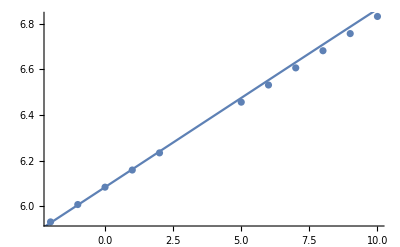

```mathematica
Show[ListPlot[{{-2,5.932},{-1,6.008},{0,6.084},{1, 6.159},{2,6.234},{5,6.456},{6, 6.531},{7, 6.606},{8,6.681}, {9, 6.756},{10, 6.831}}],Plot[(12.5 2.718281828459045^(0.025 x))/(1.05456936226167+1. 2.718281828459045^(0.025 x)),{x,-4,12}]]
```

This model does a good job describing the data as it accuratly represents the data with respect to the amount of the growing population and the limit in which the environment can sustain the panda population. It is better than our first model for representing the data as it more closely matches the data at t = 10

### 12) What assumptions are you making by using an logistical model? What factors are you not taking into consideration when using this model?

The assumption we make is that the birth and death rate are consistant year to year, we are not considering factors that could cause the death rate to increase such as poaching , or other environmental factors that will cause the panda population to decrease.

### 13) Lets assume r = 0.002 and N = 12.5 as in the last example. Use mathematica to create a slope field when 20 pandas are being poached each year. Describe the changes that you see in the slope field and interpret what they mean in terms of the panda’s population over the course of several decades. Explain your answer.

H represents the constant number of individuals being removed from the population, 20 pandas are being poached each year, the amount of pandas is represented in the millions so H = .00002

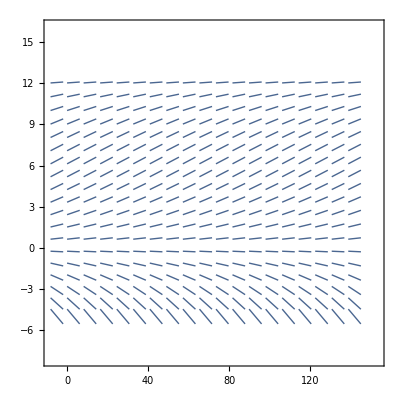

```mathematica
VectorPlot[{1,.002*y*(12.5-y)-.00002},{x,-5,150},{y,-5,13},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

As we can see even though the amount of pandas being poached each year is 20 the population growth rate is higher than the amount of poaching being done.

### 14) Use mathematica to create a slope field when 150 pandas are being poached each year, Describe the changes that you see in the slope field and interpret what they mean in terms of the panda’s population over the course of several decades. Explain your answer

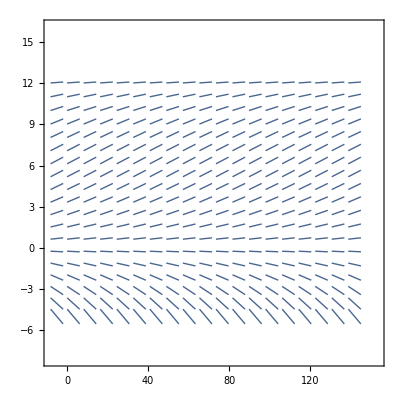

```mathematica
VectorPlot[{1,.002*y*(12.5-y)-0.000150},{x,-5,150},{y,-5,13},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

The changes are hard to see but they are there. The pandas population is continuing to grow but it is growing and a slower rate then the total amount of pandas being born into the population. This can be confirmed by looking at how many pandas are being born into the population versus how many are being poached

Part #2: Application

### 1) let t represent the time, measured in 100’s of years, where t = 0 represents the year 1800. Create a chart which lists t , the corresponding year, and the population for your country.

```mathematica
{{t, year, population}, {0, 1800, 5236631}, {0.1, 1810, 7239881}, {0.2, 1820, 9638453}, {0.3, 1830, 12886020}, {0.4, 1840, 17069453}, {0.5, 1850, 23191876}, {0.6, 1860, 31443321}, {0.7, 1870, 38558371}, {0.8, 1880, 49371340}, {0.9, 1890, 62979766}, {1.0, 1900, 76212168}, {1.1, 1910, 92228531}, {1.2, 1920, 106021568}, {1.3, 1930, 123202660}, {1.4, 1940, 132165129}, {1.5, 1950, 151325798}, {1.6, 1960, 179323175}, {1.7, 1970, 203211926}, {1.8, 1980, 226545805}, {1.9, 1990, 248709873}, {2.0, 2000, 281421906}, {2.1, 2010, 308745538}}
```

### 2) Recall the general solution for the logistical growth differential equation is given by : dP/dt= rP(t)(N-P(t)) which you found in question 7 of part 1. Find the particular solution (that is, find N, r and a) for the initial value problem using the population from 1800, 1900, 2000

```mathematica
Solve [n/(ⅇ^(-r*n*0)*c+1)==5.236,c]
```

{{c→0.000763942 (-1309.+250. n)}}

Using this information we can see that N is not a factor for the growth of the country as the environmental barrior of our population size is unkown. We can see this by plugging c back into our equation that we are given that the statement is true and as such N can take on any value. The UN projects the population of the US to be 402 million in 2050. I think with the singularity to happen around 2050 that the robots will stop us from growing past 500 million as we will take up to much space. So N = 500. This allows us to solve for C now so

```mathematica
Solve[500/(ⅇ^(-r*n*0)*c+1)==5.236, c]
```

{{c→94.4927}}

Our C is 94.4927 so then it allows us to be able to solve for r

```mathematica
Solve[500/(ⅇ^(-r*500*1)*94.4927+1)==76.212, r]
```

{{r→0.00566562}}

This gives us our r to be 0.00566562

### 3) Graph P(t) along with each of your points given by (t, population) from your data. (three of your points should lie exactly on the graph)

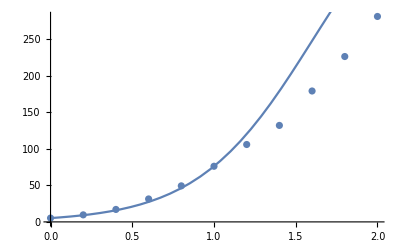

```mathematica
Show[ListPlot[{{0,5.236},{0.2,9.638},{0.4,17.069},{0.6, 31.443},{0.8,49.371},{1,76.212},{1.2, 106.021},{1.4, 132.165},{1.6,179.323}, {1.8, 226.545},{2, 281.421}}],Plot[500/(ⅇ^(-0.00566562*500*x)*94.4927+1),{x,0,3}]]
```

### 4) Analyze the fit of the model function, P(t), to the data. When was the population greater than the model predicted; when was it smaller? what could have been the cause?

The fit of my grah is good and models the growth rate of america fairly well, the problem is that right around the 1930 (represented by 1.3) the model then overtakes the trend of americas growth and eventually causes error for the later years.The factors that could cause such error is the biggest factor which is the great depression which happend in 1929, not to mention the 2nd great war happening in the 1940s which caused the population growth to be lower than normal. In addition the first couple of values (before t = 1.1) are times of american development and growth, causing immigration which then in turn will increase the population growth skewing numbers later on in history when immigration is lower. If we look at the demmographics for the united states we can see that since the 1800 up untill 1910 the population growth was above 20% after then the maximum population growth only reached 18.5% in the 1960s. This would explain why our error after 1910 (t = 1.1) is so high

### 5) What does the model predict for P(2.1); that is, the population in 2010? Compare your model’s prediction to the actual census data in 2010

```mathematica
500/(ⅇ^(-0.00566562*500*2.1)*94.4927+1)
```

401.122

As we can see our model predicts that the population by 2010 will be 401.122 and the census data tells us that the population in 2010 was 321.729

```mathematica
401.122 - 321.729
```

79.393

we can see that our model has an error of about 80 million people

### 6) What does the model predict for the population in 2100? 3100? Do these seem reasonable? explain

```mathematica
500/(ⅇ^(-0.00566562*500*3)*94.4927+1)
```

490.554

Our model predicts that by the year 2100 that the population of the US will be about 490.554

```mathematica
500/(ⅇ^(-0.00566562*500*13)*94.4927+1)
```

500.

Our model predicts that by the year 3100 that the population of the US will be at its maximum at 500 million

These numbers seem to shoot up to a degree of disbelief, if we removed the maximum population limit then these numbers would be extremly high, we would probably reach the limit of 500 million sometime quickly in the 22nd century

### 7) Now fit a simple exponential model p(t) = ce^rt to the same data. Using two points for the years 1900 and 1940 to evaluate the parameters r and c. What does this model predict the population to be in 2010, 2100, 3100? Does this seem more or less reasonable than the result for the logistic growth model P(t)

For this new model we will be using 1900 as our t = 0. Our population at 1900 is 76.212 with this information we can solve for C

```mathematica
Solve[c*ⅇ^(r*0) ==76.212,c]
```

{{c→76.212}}

Our C value is 76.212 with that information we are able to solve for r using the population of 1940 and the corresponding time (t = 0.4)

```mathematica
Solve[76.212*ⅇ^(r*0.4) ==132.165,r]
```

{{r→1.37633}}

This gives us our r value to be 1.37633. This information gives us our function p(t) = 76.212*ⅇ^(1.37633*t)

```mathematica
76.212*ⅇ^(1.37633*1.1)
```

346.361

This model tells us that the population in 2010 will be 346.361 million which is not far off with the census data being 321.729 million

```mathematica
76.212*ⅇ^(1.37633*2)
```

1195.33

This model tells us that the population in 2100 will be 1195.33 million which seems to be extreme as that is 1 billion people living in the US

```mathematica
76.212*ⅇ^(1.37633*12)
```

1.13452×10^9

Above is the number for how many people will be living in the US by the year 3100, i dont think i have to tell you how crazy that number is and why the US would not be able to support that many people. 
This model does seem to be good for predicting short term population growth but is not complex enough to represent the population as the US can only hold so many people before there is an over population problem which this model does not take into account. Both models do not take into acount the varring death and birth rates year to year and thus cannot represent to an accurate degree the population of of a country, this is however a good way to predict is the population growth rate stayed steady over the years how the population would look.

## Attached Images for solutions

Below are the images of the hand written solutions